```mathematica
(*Mathematica Code for plotting Phase trajectories*)
```

```mathematica
(* F is the dynamical system for the evolutionary dynamics in a static environment*)
(*    SetOptions[EvaluationNotebook[],ShowGroupOpener->True]  *)
```

## Deriving Invasion and Evolutionary Dynamics

```mathematica
(* These are the Vance survival functions of the zygote and gamete respectively*)
```

```mathematica
Sz[βz_,mx_,my_]:=Exp[-(βz/(mx+my))];
Sp[βp_,m_]:=Exp[-(βp/m)];
```

### Mutant of Different Mass

```mathematica
gsh=((A*M*fsh)/(ms+δm))/((A*M*fsh)/(ms+δm)+(A*M*(1-fsh))/ms);
```

```mathematica
(* gsh is the frequency of mutant gametes in the gamete pool at a given time. *)
```

```mathematica
Fshatshat=gsh^2*((A*M*fsh)/(ms+δm)+(A*M*(1-fsh))/ms)-gsh^2/(ϕ+1/((A*M*fsh)/(ms+δm)+(A*M*(1-fsh))/ms));
```

```mathematica
(* Number of \hat{s} gametes in the zygote pool that have fertilised with \hat{s} gametes *)
```

```mathematica
Fshats=gsh*(1-gsh)*((A*M*fsh)/(ms+δm)+(A*M*(1-fsh))/ms)-(gsh*(1-gsh))/(ϕ+1/((A*M*fsh)/(ms+δm)+(A*M*(1-fsh))/ms));
```

```mathematica
(* Number of \hat{s} gametes in the zygote pool that have fertilised with s gametes *)
```

```mathematica
Fss=(1-gsh)^2*((A*M*fsh)/(ms+δm)+(A*M*(1-fsh))/ms)-(1-gsh)^2/(ϕ+1/((A*M*fsh)/(ms+δm)+(A*M*(1-fsh))/ms));
```

```mathematica
(* Number of s gametes in the zygote pool that have fertilised with s gametes *)
Nshat=gsh/(ϕ+((A*M*fsh)/(ms+δm)+(A*M*(1-fsh))/ms)^(-1));
(* Number of \hat{s} gametes in the gamete pool *)
Ns=(1-gsh)/(ϕ+((A*M*fsh)/(ms+δm)+(A*M*(1-fsh))/ms)^(-1));
(* Number of s gametes in the gamete pool *)
```

```mathematica
Wshat=(Fshatshat*Sz[β,ms+δm,ms+δm]+Fshats*Sz[β,ms,ms+δm])*(1-Cz)+Nshat*Sp[β,ms+δm]*(1-Cp);
Ws=(Fss*Sz[β,ms,ms] + Fshats*Sz[β,ms,ms+δm])*(1-Cz) +Ns*Sp[β,ms]*(1-Cp);
(* absolute fitness functions of \hat{s} and s respectively *)
fshprime=Wshat/(Wshat+Ws);
```

```mathematica
(*the line below outputs the equation for the invasion dynamics*)
```

```mathematica
DfshprimeDdeltam=(D[fshprime,δm]/.δm->0)//FullSimplify;
```

### Mutant of Different Encounter Rate

```mathematica
Nshat0=(A*M*fsh)/ms;
(*Number of mutant gametes initially*)
Ns0=(A*M*(1-fsh))/ms;
(*Number of resident gametes initially*)
Ntot0=Nshat0+Ns0; 
(*Total number of gametes initially*)
Ntot=1/(α*T+Ntot0^(-1));
gshat0=Nshat0/(Nshat0+Ns0);
(*Initial frequency of mutant gametes*)
gshat=1-1/(1+gshat0/(1-gshat0)*(α*T*Ntot0+1)^(-δα/(2*α)));
(* gshat is the frequency of mutant gametes in the gamete pool at a given time. *)
Nshat=Ntot*gshat;
(* Number of \hat{s} gametes in the gamete pool *)
Ns=Ntot(1-gshat);
(* Number of s gametes in the gamete pool *)
Fshat=Nshat0-Nshat;
Fs=Ns0-Ns;
(*Number of mutant and resident gametes in the gamete pool respectively*)
wshat=Fshat*Sz[β,ms,ms]*(1-Cz)+Nshat*Sp[β,ms]*(1-Cp);
ws=Fs*Sz[β,ms,ms]*(1-Cz)+Ns*Sp[β,ms]*(1-Cp);
fshprime=wshat/(ws+wshat);
(D[fshprime,δα]/.δα->0)//FullSimplify
```

-((1-Cp+(-1+Cz) ⅇ^(β/(2 ms))) (-1+fsh) fsh ms Log[1+(A M T α)/ms])/(2 α ((-1+Cp) ms+A (-1+Cz) ⅇ^(β/(2 ms)) M T α))

## Static Environment

### Phase Trajectories

```mathematica
F={
-((4m(m-β)(1-Cp)-A(-1+Cz)Exp[β/(2m)]M(4m-β)α*T)/(4 m^2(m(1-Cp)-A(-1+Cz)Exp[β/(2m)]M*α*T))),
(((1-Cp)+(Cz-1)Exp[β/(2m)])m*Log[1+(A*M*α*T)/m])/(2α(A(Cz-1)Exp[β/(2m)]*M*T*α-m(1-Cp)))
};
```

```mathematica
(* params are the parameters of the dynamical system above. The cost of fertilisation here is denoted as Cz and cost to parthenogenic route is Cp. *)
```

```mathematica
params={A->100,M->1,T->0.1,Cz->0.3,Cp->0.5,β->1};
```

```mathematica
(*Below we plot numerical solutions to F to plot sample phase trajectories*)
```

```mathematica
nSol3=NDSolve[{
m'[t]==(F[[1]]/.params/.{m->m[t],α->α[t]}),
α'[t]==(F[[2]]/.params/.{m->m[t],α->α[t]}),
m[0]==0.5,
α[0]==0.001
},{m[t],α[t]},{t,0,100}];
```

```mathematica
Show[
StreamPlot[F/.params,{m,0,2},{α,0,1},StreamStyle->Gray],
ParametricPlot[{m[t],α[t]}/.nSol3,{t,0,100},PlotStyle->Purple]]
```

## Switching Environment

### Phase Trajectories

```mathematica
(* FSW is the dynamical system for the evolutionary dynamics in a switching environment with fixed time in each environment*)
```

```mathematica
FSW={-(4m(1-Cp)(m-βB)-A(-1+Cz)Exp[βB/(2m)]M(4m-βB)ϕ)/(4 m^2(m(1-Cp)-A(-1+Cz)Exp[βB/(2m)]M*ϕ))*λGB/(λBG+λGB)+-(4m(1-Cp)(m-βG)-A(-1+Cz)Exp[βG/(2m)]M(4m-βG)ϕ)/(4 m^2(m(1-Cp)-A(-1+Cz)Exp[βG/(2m)]M*ϕ))*λBG/(λBG+λGB),
(((1-Cp)+(Cz-1)Exp[βB/(2m)])m*Log[1+(A*M*α*T)/m])/(2α(A(Cz-1)Exp[βB/(2m)]*M*T*α-m(1-Cp)))*λGB/(λBG+λGB)+(((1-Cp)+(Cz-1)Exp[βG/(2m)])m*Log[1+(A*M*α*T)/m])/(2α(A(Cz-1)Exp[βG/(2m)]*M*T*α-m(1-Cp)))*λBG/(λBG+λGB)}/.{ϕ->α*T};
```

```mathematica
(* params are the parameters of the dynamical system above. The cost of fertilisation here is denoted as Cz and cost to parthenogenic route is Cp. *)
```

```mathematica
params={A->100,M->10,T->0.1,Cz->0.35,Cp->0.1,βB->3, βG->0.01,λGB->1, λBG->2.1};
```

```mathematica
(*Below we plot numerical solutions to FSW to plot sample phase trajectories*)
```

```mathematica
nSol1SW=NDSolve[{
m'[t]==(FSW[[1]]/.params/.{m->m[t],α->α[t]}),
α'[t]==(FSW[[2]]/.params/.{m->m[t],α->α[t]}),
m[0]==0.6,
α[0]==0.3
},{m[t],α[t]},{t,0,100000}];

nSol2SW=NDSolve[{
m'[t]==(FSW[[1]]/.params/.{m->m[t],α->α[t]}),
α'[t]==(FSW[[2]]/.params/.{m->m[t],α->α[t]}),
m[0]==0.1,
α[0]==0.1
},{m[t],α[t]},{t,0,1000}];

nSol3SW=NDSolve[{
m'[t]==(FSW[[1]]/.params/.{m->m[t],α->α[t]}),
α'[t]==(FSW[[2]]/.params/.{m->m[t],α->α[t]}),
m[0]==0.2955,
α[0]==0.2254
},{m[t],α[t]},{t,0,1000}];
```

LessEqual::nord: Invalid comparison with -0.0542941-2.73111×10^-10 ⅈ attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

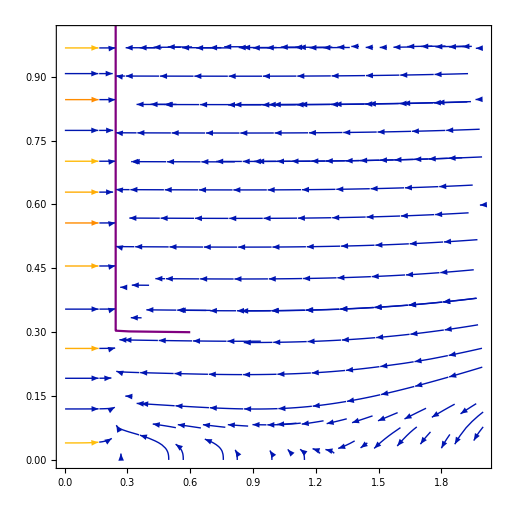

```mathematica
Show[StreamPlot[FSW/.params,{m,0,2},{α,0,1},StreamStyle->Gray],
	ParametricPlot[{m[t],α[t]}/.nSol1SW,{t,0,1000},PlotStyle->Purple]]
```

### Deriving Switching Induced Fixed Point

```mathematica
(*Here, we solve the first equation of FSW in terms of α to calculate α^{*} *)
params={A->10,M->10,T->1,Cz->0.3,Cp->0,βB->4, βG->0.002,λGB->1, λBG->2.4};
```

```mathematica
αstar=Solve[((1-Cp+(-1+Cz) ⅇ^(βB/(2 m)))  m Log[1+(A M T α)/m])/(2 α ((-1+Cp) m+A (-1+Cz) ⅇ^(βB/(2 m)) M T α))*λGB/(λBG+λGB)+((1-Cp+(-1+Cz) ⅇ^(βG/(2 m))) m Log[1+(A M T α)/m])/(2 α ((-1+Cp) m+A (-1+Cz) ⅇ^(βG/(2 m)) M T α))*λBG/(λBG+λGB)==0,α]//FullSimplify;
```

```mathematica
(* Here we approximate the value of m^{*} by taking the limit as ϕ -> infinity, then solving for m in the equation dmdτ *)
```

```mathematica
dmdτϕInf=Limit[-(4m(m-βB)(1-Cp)-A(-1+Cz)Exp[βB/(2m)]M(4m-βB)α*T)/(4 m^2(m(1-Cp)-A(-1+Cz)Exp[βB/(2m)]M*α*T))*λGB/(λBG+λGB)+-(4m(m-βG)-A(-1+C0)M(4m-βG)α*T)/(4 m^2(m(1-Cp)-A(-1+C0)M*α*T))*λBG/(λBG+λGB),T->Infinity];
```

```mathematica
mstar=Solve[dmdτϕInf==0,m];
```

```mathematica
(* αstar and mstar is the approximation of the switching induced fixed point *)
```

```mathematica
αstar[[1,1,2]]/.{m->mstar[[1,1,2]]}/.params
```

### Checking the Stability of the Switching Induced Fixed Point

```mathematica
(* a is a vector containing the dependent variables in the ODEs of the dynamical system *)
```

```mathematica
a={m,α};
equilib={α->((λBG+(-1+C0) ⅇ^((2 βG (λBG+λGB))/(βG λBG+βB λGB)) λBG+λGB+(-1+C0) ⅇ^((2 βB (λBG+λGB))/(βG λBG+βB λGB)) λGB) (βG λBG+βB λGB))/(4 A (-1+C0) M T (λBG+λGB) (ⅇ^((2 βB (λBG+λGB))/(βG λBG+βB λGB)) λBG+ⅇ^((2 βG (λBG+λGB))/(βG λBG+βB λGB)) (λGB+(-1+C0) ⅇ^((2 βB (λBG+λGB))/(βG λBG+βB λGB)) (λBG+λGB))))/.params, m->(βB λGB+βG λBG)/(4 (λBG+λGB))/.params};
```

```mathematica
(* j is the Jacobian of the dynamical system evaluated at the equilibrium point *)
```

```mathematica
j=(D[(FSW/.params),{a}]/.equilib);
```

```mathematica
(* eigenvalues of the Jacobian *)
```

```mathematica
EigJ=Eigenvalues[j];
```

Eigenvalues[{0,0}/.{α→((λBG+(-1+C0) ⅇ^((2 βG (λBG+λGB))/(βG λBG+βB λGB)) λBG+λGB+(-1+C0) ⅇ^((2 βB (λBG+λGB))/(βG λBG+βB λGB)) λGB) (βG λBG+βB λGB))/(4 A (-1+C0) M T (λBG+λGB) (ⅇ^((2 βB (λBG+λGB))/(βG λBG+βB λGB)) λBG+ⅇ^((2 βG (λBG+λGB))/(βG λBG+βB λGB)) (λGB+(-1+C0) ⅇ^((2 βB (λBG+λGB))/(βG λBG+βB λGB)) (λBG+λGB))))/.params,m→(βG λBG+βB λGB)/(4 (λBG+λGB))/.params}]

```mathematica
{-1.7928265823563359,-0.0027055795138278904}
```

{-1.79283,-0.00270558}

## Evolutionary Branching

```mathematica
Disruptiveness=D[(D[fshprime,{δm,2}]/.δm->0),fsh]/.{fsh->0}//FullSimplify;
```

```mathematica
FitnessGradient=D[D[fshprime,δm]/.{δm->0},fsh]/.{fsh->0,ϕ->α*T}//FullSimplify;
```

```mathematica
Solve[{FitnessGradient==0,Disruptiveness==0},{ms,α}]
```